## Set up

Add directory to data file here

```mathematica
dir=SetDirectory["/Users/renata/Documents/Kita/Translation/"];
```

```mathematica
cod={"AAA","AAC","AAG","AAT","ACA","ACC","ACG","ACT","AGA","AGC","AGG","AGT","ATA","ATC","ATG","ATT","CAA","CAC","CAG","CAT","CCA","CCC","CCG","CCT","CGA","CGC","CGG","CGT","CTA","CTC","CTG","CTT","GAA","GAC","GAG","GAT","GCA","GCC","GCG","GCT","GGA","GGC","GGG","GGT","GTA","GTC","GTG","GTT","TAA","TAC","TAG","TAT","TCA","TCC","TCG","TCT","TGA","TGC","TGG","TGT","TTA","TTC","TTG","TTT"};
```

Data should be in the format:
gene name
codons
raw densities

```mathematica
data=Import["Rib_dens_data.txt","Table"];
```

```mathematica
ps=Table[i,{i,1,Length[data],3}];
```

```mathematica
gns=Flatten[data[[ps]]];
```

```mathematica
Length[gns]
```

850

```mathematica
train=Sort[RandomSample[Table[i,{i,Length[gns]}],Round[(2/3)*Length[gns]]]] ;
```

```mathematica
test=Complement[Table[i,{i,1Length[gns]}],train];
```

```mathematica
{Length[train],Length[test]}
```

lf - number of codons to the left from A site
rt - number of codons to the right of A site

```mathematica
lf=7; rt=5;
```

```mathematica
XX={};
For[i=1,i≤ Length[train],
c=data[[ps[[train[[i]]]]+1]];
x=Flatten[Table[Position[cod,c[[ii]]],{ii,Length[c]}]];
y=data[[ps[[train[[i]]]]+2]]/Mean[data[[ps[[train[[i]]]]+2]]];
For[j=lf+1,j≤ Length[x]-(rt+1),
trn={};
For[k=j-lf,k≤j+rt,
dg=Table[0,{kk,Length[cod]}];
dg[[x[[k]]]]=1;
AppendTo[trn,dg];
k++];
AppendTo[XX,Flatten[{trn,y[[j]]}]];
j++];
i++]
```

```mathematica
dt=Table[XX[[i,;;(-2)]]->XX[[i,-1]],{i,Length[XX]}];
```

## ML

#### Neural Network

```mathematica
p=Predict[dt,Method->"NeuralNetwork"]
```

```mathematica
pr={};YY={};
For[i=1,i≤ Length[test],
c=data[[ps[[test[[i]]]]+1]];
x=Flatten[Table[Position[cod,c[[ii]]],{ii,Length[c]}]];
y=data[[ps[[test[[i]]]]+2]]/Mean[data[[ps[[test[[i]]]]+2]]];
For[j=lf+1,j≤ Length[x]-(rt+1),
trn={};
For[k=j-lf,k≤j+rt,
dg=Table[0,{kk,Length[cod]}];
dg[[x[[k]]]]=1;
AppendTo[trn,dg];
k++];
tmp=p[Flatten[trn]];
AppendTo[pr,{y[[j]],Max[0,tmp]}];
AppendTo[YY,Flatten[{trn,y[[j]]}]];
j++];
i++]
```

```mathematica
Correlation[pr[[;;,1]],pr[[;;,2]]]
```

0.496767

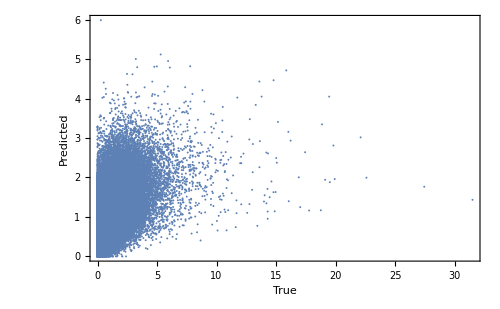

```mathematica
ListPlot[pr,Frame->True,FrameLabel->{"True","Predicted"},PlotRange->All,ImageSize->500]
```

#### Linear regression

```mathematica
p=Predict[dt,Method->"LinearRegression"]
```

```mathematica
pr={};YY={};
For[i=1,i≤ Length[test],
c=data[[ps[[test[[i]]]]+1]];
x=Flatten[Table[Position[cod,c[[ii]]],{ii,Length[c]}]];
y=data[[ps[[test[[i]]]]+2]]/Mean[data[[ps[[test[[i]]]]+2]]];
For[j=lf+1,j≤ Length[x]-(rt+1),
trn={};
For[k=j-lf,k≤j+rt,
dg=Table[0,{kk,Length[cod]}];
dg[[x[[k]]]]=1;
AppendTo[trn,dg];
k++];
tmp=p[Flatten[trn]];
AppendTo[pr,{y[[j]],Max[0,tmp]}];
AppendTo[YY,Flatten[{trn,y[[j]]}]];
j++];
i++]
```

```mathematica
Correlation[pr[[;;,1]],pr[[;;,2]]]
```

0.43612

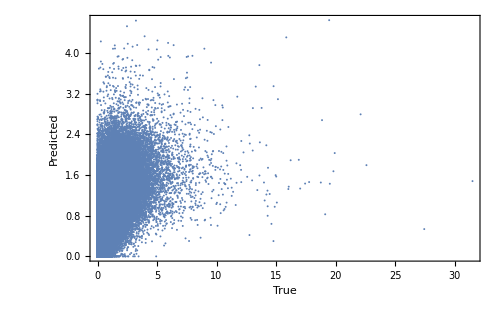

```mathematica
ListPlot[pr,Frame->True,FrameLabel->{"True","Predicted"},PlotRange->All,ImageSize->500]
```

#### Random Forest

```mathematica
p=Predict[dt,Method->"RandomForest"]
```

```mathematica
pr={};YY={};
For[i=1,i≤ Length[test],
c=data[[ps[[test[[i]]]]+1]];
x=Flatten[Table[Position[cod,c[[ii]]],{ii,Length[c]}]];
y=data[[ps[[test[[i]]]]+2]]/Mean[data[[ps[[test[[i]]]]+2]]];
For[j=lf+1,j≤ Length[x]-(rt+1),
trn={};
For[k=j-lf,k≤j+rt,
dg=Table[0,{kk,Length[cod]}];
dg[[x[[k]]]]=1;
AppendTo[trn,dg];
k++];
tmp=p[Flatten[trn]];
AppendTo[pr,{y[[j]],Max[0,tmp]}];
AppendTo[YY,Flatten[{trn,y[[j]]}]];
j++];
i++]
```

```mathematica
Correlation[pr[[;;,1]],pr[[;;,2]]]
```

0.392796

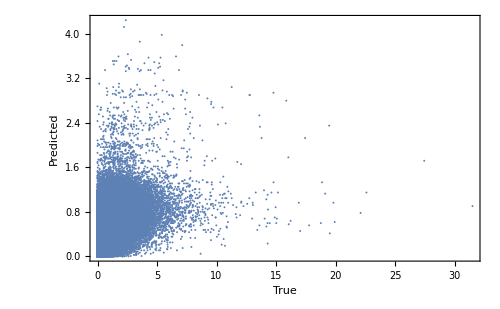

```mathematica
ListPlot[pr,Frame->True,FrameLabel->{"True","Predicted"},PlotRange->All,ImageSize->500]
```

#### Nearest Neighbours

```mathematica
p=Predict[dt,Method->"NearestNeighbors"]
```

```mathematica
pr={};YY={};
For[i=1,i≤ Length[test],
c=data[[ps[[test[[i]]]]+1]];
x=Flatten[Table[Position[cod,c[[ii]]],{ii,Length[c]}]];
y=data[[ps[[test[[i]]]]+2]]/Mean[data[[ps[[test[[i]]]]+2]]];
For[j=lf+1,j≤ Length[x]-(rt+1),
trn={};
For[k=j-lf,k≤j+rt,
dg=Table[0,{kk,Length[cod]}];
dg[[x[[k]]]]=1;
AppendTo[trn,dg];
k++];
tmp=p[Flatten[trn]];
AppendTo[pr,{y[[j]],Max[0,tmp]}];
AppendTo[YY,Flatten[{trn,y[[j]]}]];
j++];
i++]
```

```mathematica
Correlation[pr[[;;,1]],pr[[;;,2]]]
```

0.307008

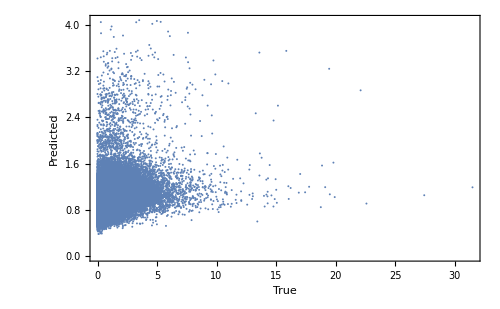

```mathematica
ListPlot[pr,Frame->True,FrameLabel->{"True","Predicted"},PlotRange->All,ImageSize->500]
```